```mathematica
(*Problem 1*)
```

```mathematica
m1 = {{-4, -1, 0, 0}, {-3, -α, δ, 0}, {-4, a, (b-4), 1}, {0, λ α, (ν-λ δ), -1}}
```

{{-4,-1,0,0},{-3,-α,δ,0},{-4,a,-4+b,1},{0,α λ,-δ λ+ν,-1}}

```mathematica
b1 = {-2, -1, -1, -1}
```

{-2,-1,-1,-1}

```mathematica
sol1 = LinearSolve[m1, b1]
```

{(4-b-8 α+2 b α+2 δ+2 a δ+δ λ-ν+2 α ν)/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),(2 (4-b+δ λ-ν))/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),(2 (1+a+α λ))/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),(12-3 b-16 α+4 b α+4 δ+4 a δ+8 α λ-2 b α λ+δ λ-2 a δ λ-ν+2 a ν+4 α ν)/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν)}

```mathematica
sol1/.{a-> 0, b-> 0, α-> 1, δ-> 1, ϕ-> 1}//Simplify
```

{(-2+λ+ν)/(3 λ+ν),(2 (4+λ-ν))/(3 λ+ν),(2 (1+λ))/(3 λ+ν),3}

```mathematica
b2 = {0, ϕ, 0, -λ ϕ}
```

{0,ϕ,0,-λ ϕ}

```mathematica
sol2 = LinearSolve[m1, b2]
```

{(-4 ϕ+b ϕ+ν ϕ)/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),-(4 (-4 ϕ+b ϕ+ν ϕ))/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),(4 ϕ+4 a ϕ+3 λ ϕ)/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν),(12 λ ϕ-3 b λ ϕ+4 ν ϕ+4 a ν ϕ)/(12-3 b-16 α+4 b α+4 δ+4 a δ+3 δ λ-3 ν+4 α ν)}

```mathematica
sol2/.{a-> 0, b-> 0, α-> 1, δ-> 1, ϕ-> 1}//Simplify
```

{(-4+ν)/(3 λ+ν),-(4 (-4+ν))/(3 λ+ν),(4+3 λ)/(3 λ+ν),4}

```mathematica
(*Problem 3*)
```

```mathematica
Subscript[T, c] = Subscript[μ, e]/R(Const G M^(2/3)Subscript[ρ, c]^(1/3)- Kconst Subscript[ρ, c]^(γ-1)/Subscript[μ, e]^γ )
```

(μ_e (Const G M^(2/3) ρ_c^(1/3)-Kconst μ_e^-γ ρ_c^(-1+γ)))/R

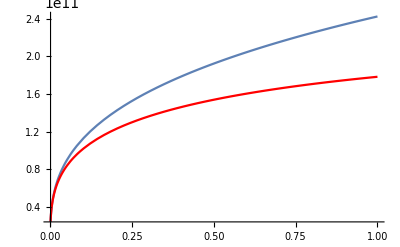

```mathematica
Show[Plot[Subscript[T, c]/.{R-> 8.3 10^7,Subscript[μ, e]-> 2.0, G-> 6.67 10^-8,M-> 1.989 10^33, Const -> 10, Kconst-> 1.24 10^15, γ-> 4/3}, {Subscript[ρ, c],10^6, 10^9}],
Plot[Subscript[T, c]/.{R-> 8.3 10^7,Subscript[μ, e]-> 2.0, G-> 6.67 10^-8,M-> 1.989 10^33, Const -> 10, Kconst-> 10^13, γ-> 5/3}, {Subscript[ρ, c],10^6, 10^9},PlotStyle->Red]]
```